```mathematica
r^2=x^2+y^2
Subscript[r, x]=x/r=(r Cos[t])/r=Cos[t]
Subscript[r, y]=y/r=Sin[t]
 Subscript[t, x] = -(Cos[t]^2 y)/x^2= -Sin[t]/r
Subscript[t, y]=Cos[t]^2/x=Cos[t]/r

Subscript[u, x]=Subscript[u, r] Subscript[r, x]+Subscript[u, t] Subscript[t, x] =Subscript[u, r] Cos[t]-Subscript[u, t] Sin[t]/r 
Subscript[u, y]=Subscript[u, r] Subscript[r, y]+Subscript[u, t] Subscript[t, y] =Subscript[u, r] Sin[t]+Subscript[u, t] Cos[t]/r 
Subscript[u, xx]=Subscript[(Subscript[u, r] Cos[t]-Subscript[u, t] Sin[t]/r  ), x]=Subscript[(Subscript[u, r] Cos[t]-Subscript[u, t] Sin[t]/r ), r] Cos[t]-Subscript[(Subscript[u, r] Cos[t]-Subscript[u, t] Sin[t]/r ), t] Sin[t]/r =
(Subscript[u, rr] Cos[t]-Subscript[u, rt] Sin[t]/r+Subscript[u, t] Sin[t]/r^2 )Cos[t]-(Subscript[u, rt] Cos[t]-Subscript[u, r] Sin[t]-Subscript[u, tt] Sin[t]/r-Subscript[u, t] Cos[t]/r )Sin[t]/r =
Subscript[u, rr] Cos[t]^2+Subscript[u, tt] Sin[t]^2/r^2-2 Subscript[u, rt](Cos[t]Sin[t])/r +Subscript[u, r] Sin[t]^2/r+2 Subscript[u, t](Sin[t]Cos[t])/r^2
Subscript[u, yy]=Subscript[(Subscript[u, r] Sin[t]+Subscript[u, t] Cos[t]/r ), y]=Subscript[(Subscript[u, r] Sin[t]+Subscript[u, t] Cos[t]/r ), r] Sin[t]+Subscript[(Subscript[u, r] Sin[t]+Subscript[u, t] Cos[t]/r ), t] Cos[t]/r=
(Subscript[u, rr] Sin[t]+Subscript[u, rt] Cos[t]/r-Subscript[u, t] Cos[t]/r^2 )Sin[t]+(Subscript[u, rt] Sin[t]+Subscript[u, r] Cos[t]+Subscript[u, tt] Cos[t]/r-Subscript[u, t] Sin[t]/r )Cos[t]/r=Subscript[u, rr] Sin[t]^2+Subscript[u, tt] Cos[t]^2/r^2+2 Subscript[u, rt](Cos[t]Sin[t])/r-2 Subscript[u, t](Cos[t]Sin[t])/r^2+Subscript[u, r] Cos[t]^2/r

Subscript[(a (x,y)Subscript[u, x]), x]=Subscript[(a (x,y)Subscript[u, x]), r] Cos[t]-Subscript[(a (x,y)Subscript[u, x]), t] Sin[t]/r=
(Subscript[a, r] (Subscript[u, r] Cos[t]-Subscript[u, t] Sin[t]/r)+a (Subscript[u, rr] Cos[t]-Subscript[u, rt] Sin[t]/r-Subscript[u, t] Sin[t]/r^2))Cos[t]-(Subscript[a, t] (Subscript[u, r] Cos[t]-Subscript[u, t] Sin[t]/r)+a(Subscript[u, rt] Cos[t]-Subscript[u, r] Sin[t]-Subscript[u, tt] Sin[t]/r-Subscript[u, t] Cos[t]/r))Sin[t]/r
Subscript[(b(x,y)Subscript[u, y]), y]=Subscript[(b (x,y)Subscript[u, y]), r] Sin[t]+Subscript[(b (x,y)Subscript[u, y]), t] Cos[t]/r=(Subscript[b, r] (Subscript[u, r] Sin[t]+Subscript[u, t] Cos[t]/r)+b (Subscript[u, rr] Sin[t]+Subscript[u, rt] Cos[t]/r-Subscript[u, t] Sin[t]/r))Sin[t]+(Subscript[b, t] (Subscript[u, r] Sin[t]+Subscript[u, t] Cos[t]/r)+b (Subscript[u, rt] Sin[t]+Subscript[u, r] Cos[t]+Subscript[u, tt] Cos[t]/r-Subscript[u, t] Sin[t]/r))Cos[t]/r
```

```mathematica
(Subscript[a, r] (Subscript[u, r] Cos[t]-Subscript[u, t] Sin[t]/r)+a (Subscript[u, rr] Cos[t]-Subscript[u, rt] Sin[t]/r-Subscript[u, t] Sin[t]/r^2))Cos[t]-(Subscript[a, t] (Subscript[u, r] Cos[t]-Subscript[u, t] Sin[t]/r)+a(Subscript[u, rt] Cos[t]-Subscript[u, r] Sin[t]-Subscript[u, tt] Sin[t]/r-Subscript[u, t] Cos[t]/r))Sin[t]/r+(Subscript[b, r] (Subscript[u, r] Sin[t]+Subscript[u, t] Cos[t]/r)+b (Subscript[u, rr] Sin[t]+Subscript[u, rt] Cos[t]/r-Subscript[u, t] Sin[t]/r))Sin[t]+(Subscript[b, t] (Subscript[u, r] Sin[t]+Subscript[u, t] Cos[t]/r)+b (Subscript[u, rt] Sin[t]+Subscript[u, r] Cos[t]+Subscript[u, tt] Cos[t]/r-Subscript[u, t] Sin[t]/r))Cos[t]/r//FullSimplify
```

1/r^2(r (b Cos[t]^2+a Sin[t]^2+r Cos[t]^2 a_r+Sin[t] (r Sin[t] b_r+Cos[t] (-a_t+b_t))) u_r+r^2 (a Cos[t]^2+b Sin[t]^2) u_rr-2 a r Cos[t] Sin[t] u_rt+b r Sin[2 t] u_rt-b Cos[t] Sin[t] u_t-b r Sin[t]^2 u_t-r Cos[t] Sin[t] a_r u_t+Sin[t]^2 a_t u_t+r Cos[t] Sin[t] b_r u_t+Cos[t]^2 b_t u_t+(b Cos[t]^2+a Sin[t]^2) u_tt)

```mathematica
D[ArcTan[y/x],x]
D[Tan[t],t]==1/Cos[t]^2
```

-y/(x^2 (1+y^2/x^2))

True

```mathematica
Cos[ArcTan[t]]
```

1/(√(1+t^2))

```mathematica
Solve[a(Subscript[u, rr] Cos[t]^2+Subscript[u, tt] Sin[t]^2/r^2-2 Subscript[u, rt](Cos[t]Sin[t])/r +Subscript[u, r] Sin[t]^2/r+2 Subscript[u, t](Sin[t]Cos[t])/r^2)+b(Subscript[u, rr] Sin[t]^2+Subscript[u, tt] Cos[t]^2/r^2+2 Subscript[u, rt](Cos[t]Sin[t])/r-2 Subscript[u, t](Cos[t]Sin[t])/r^2+Subscript[u, r] Cos[t]^2/r)+(Subscript[a, r] +Sin[t]^2 (Subscript[b, r] - Subscript[a, r]) +(Cos[t] Sin[t])/r(Subscript[b, t]-Subscript[a, t])) Subscript[u, r]+(Subscript[a, t]/r^2+Cos[t]^2/r^2(Subscript[b, t] -Subscript[a, t])+(Subscript[a, r]+Subscript[b, r])(Cos[t] Sin[t])/r)Subscript[u, t]-σ u==f,Subscript[u, rr]]
```

{{u_rr→1/(r^2 (a Cos[t]^2+b Sin[t]^2))(f r^2+r^2 u σ-b r Cos[t]^2 u_r-a r Sin[t]^2 u_r-r^2 a_r u_r+r^2 Sin[t]^2 a_r u_r+r Cos[t] Sin[t] a_t u_r-r^2 Sin[t]^2 b_r u_r-r Cos[t] Sin[t] b_t u_r+2 a r Cos[t] Sin[t] u_rt-2 b r Cos[t] Sin[t] u_rt-2 a Cos[t] Sin[t] u_t+2 b Cos[t] Sin[t] u_t-r Cos[t] Sin[t] a_r u_t-a_t u_t+Cos[t]^2 a_t u_t-r Cos[t] Sin[t] b_r u_t-Cos[t]^2 b_t u_t-b Cos[t]^2 u_tt-a Sin[t]^2 u_tt)}}

```mathematica
(f+u σ)/(a Cos[t]^2+b Sin[t]^2)-1/(a Cos[t]^2+b Sin[t]^2)(Subscript[a, r] +Sin[t]^2 (Subscript[b, r] - Subscript[a, r]) +(Cos[t] Sin[t])/r(Subscript[b, t]-Subscript[a, t])+(b  Cos[t]^2 +a  Sin[t]^2)/r) Subscript[u, r]-1/(a Cos[t]^2+b Sin[t]^2)((Subscript[a, t] Sin[t]^2+Subscript[b, t] Cos[t]^2)/r^2+(Subscript[a, r]+Subscript[b, r])(Cos[t] Sin[t])/r+(2( a - b )Cos[t] Sin[t])/r^2)Subscript[u, t]+(2( a   - b)Cos[t] Sin[t] Subscript[u, rt])/(r (a Cos[t]^2+b Sin[t]^2))-((b Cos[t]^2 +a Sin[t]^2 )Subscript[u, tt])/(r^2 (a Cos[t]^2+b Sin[t]^2))==1/(r^2 (a Cos[t]^2+b Sin[t]^2))(f r^2+r^2 u σ-b r Cos[t]^2 Subscript[u, r]-a r Sin[t]^2 Subscript[u, r]-r^2 Subscript[a, r] Subscript[u, r]+r^2 Sin[t]^2 Subscript[a, r] Subscript[u, r]+r Cos[t] Sin[t] Subscript[a, t] Subscript[u, r]-r^2 Sin[t]^2 Subscript[b, r] Subscript[u, r]-r Cos[t] Sin[t] Subscript[b, t] Subscript[u, r]+2 a r Cos[t] Sin[t] Subscript[u, rt]-2 b r Cos[t] Sin[t] Subscript[u, rt]-2 a Cos[t] Sin[t] Subscript[u, t]+2 b Cos[t] Sin[t] Subscript[u, t]-r Cos[t] Sin[t] Subscript[a, r] Subscript[u, t]-Subscript[a, t] Subscript[u, t]+Cos[t]^2 Subscript[a, t] Subscript[u, t]-r Cos[t] Sin[t] Subscript[b, r] Subscript[u, t]-Cos[t]^2 Subscript[b, t] Subscript[u, t]-b Cos[t]^2 Subscript[u, tt]-a Sin[t]^2 Subscript[u, tt])//Simplify
```

True

```mathematica
(b  Cos[t]^2 +a  Sin[t]^2)/(a Cos[t]^2+b Sin[t]^2)==b//Reduce
(b x^2+a y^2)/(a x^2+b y^2)==b//Reduce
```

(Sin[t]==0&&b==0&&a Cos[t]≠0)||(-b Cos[t]^2+Sin[t]^2≠0&&a==(-b Cos[t]^2+b^2 Sin[t]^2)/(-b Cos[t]^2+Sin[t]^2)&&-b Cos[t]^4+b Sin[t]^4≠0)||(Sin[t]≠0&&(Cos[t]==-Sin[t]||Cos[t]==-ⅈ Sin[t]||Cos[t]==ⅈ Sin[t]||Cos[t]==Sin[t])&&Cos[t]≠0&&b==Tan[t]^2&&a Cos[t]^4+Sin[t]^4≠0)

(y==0&&b==0&&a x≠0)||(b x^2-y^2≠0&&a==(b x^2-b^2 y^2)/(b x^2-y^2)&&b x^4-b y^4≠0)||(y≠0&&(x==-y||x==-ⅈ y||x==ⅈ y||x==y)&&x≠0&&b==y^2/x^2&&a x^4+y^4≠0)

```mathematica
1/(r^2 (a Cos[t]^2+b Sin[t]^2))(f r^2+r^2 u σ-b r Cos[t]^2 Subscript[u, r]-a r Sin[t]^2 Subscript[u, r]-r^2 Subscript[a, r] Subscript[u, r]+r^2 Sin[t]^2 Subscript[a, r] Subscript[u, r]+r Cos[t] Sin[t] Subscript[a, t] Subscript[u, r]-r^2 Sin[t]^2 Subscript[b, r] Subscript[u, r]-r Cos[t] Sin[t] Subscript[b, t] Subscript[u, r]+2 a r Cos[t] Sin[t] Subscript[u, rt]-2 b r Cos[t] Sin[t] Subscript[u, rt]-2 a Cos[t] Sin[t] Subscript[u, t]+2 b Cos[t] Sin[t] Subscript[u, t]-r Cos[t] Sin[t] Subscript[a, r] Subscript[u, t]-Subscript[a, t] Subscript[u, t]+Cos[t]^2 Subscript[a, t] Subscript[u, t]-r Cos[t] Sin[t] Subscript[b, r] Subscript[u, t]-Cos[t]^2 Subscript[b, t] Subscript[u, t]-b Cos[t]^2 Subscript[u, tt]-a Sin[t]^2 Subscript[u, tt])//Expand
```

f/(a Cos[t]^2+b Sin[t]^2)+(u σ)/(a Cos[t]^2+b Sin[t]^2)-(b Cos[t]^2 u_r)/(r (a Cos[t]^2+b Sin[t]^2))-(a Sin[t]^2 u_r)/(r (a Cos[t]^2+b Sin[t]^2))-(a_r u_r)/(a Cos[t]^2+b Sin[t]^2)+(Sin[t]^2 a_r u_r)/(a Cos[t]^2+b Sin[t]^2)+(Cos[t] Sin[t] a_t u_r)/(r (a Cos[t]^2+b Sin[t]^2))-(Sin[t]^2 b_r u_r)/(a Cos[t]^2+b Sin[t]^2)-(Cos[t] Sin[t] b_t u_r)/(r (a Cos[t]^2+b Sin[t]^2))+(2 a Cos[t] Sin[t] u_rt)/(r (a Cos[t]^2+b Sin[t]^2))-(2 b Cos[t] Sin[t] u_rt)/(r (a Cos[t]^2+b Sin[t]^2))-(2 a Cos[t] Sin[t] u_t)/(r^2 (a Cos[t]^2+b Sin[t]^2))+(2 b Cos[t] Sin[t] u_t)/(r^2 (a Cos[t]^2+b Sin[t]^2))-(Cos[t] Sin[t] a_r u_t)/(r (a Cos[t]^2+b Sin[t]^2))-(a_t u_t)/(r^2 (a Cos[t]^2+b Sin[t]^2))+(Cos[t]^2 a_t u_t)/(r^2 (a Cos[t]^2+b Sin[t]^2))-(Cos[t] Sin[t] b_r u_t)/(r (a Cos[t]^2+b Sin[t]^2))-(Cos[t]^2 b_t u_t)/(r^2 (a Cos[t]^2+b Sin[t]^2))-(b Cos[t]^2 u_tt)/(r^2 (a Cos[t]^2+b Sin[t]^2))-(a Sin[t]^2 u_tt)/(r^2 (a Cos[t]^2+b Sin[t]^2))

```mathematica
Subscript[(a (x,y)Subscript[u, x]), x]=Subscript[a, x] Subscript[u, x]+a Subscript[u, xx]
Subscript[(b (x,y)Subscript[u, y]), y]=Subscript[b, y] Subscript[u, y]+b Subscript[u, yy]
Subscript[(a (x,y)Subscript[u, x]), x]+Subscript[(b (x,y)Subscript[u, y]), y]=Subscript[a, x] Subscript[u, x]+a Subscript[u, xx]+Subscript[b, y] Subscript[u, y]+b Subscript[u, yy]=a(Subscript[u, r]/r+Subscript[u, rr]+Subscript[u, tt]/r^2)+Subscript[a, x] Subscript[u, x]+Subscript[b, y] Subscript[u, y]=Subscript[u, r]/r+Subscript[u, rr]+Subscript[u, tt]/r^2+(Subscript[a, r] Cos[t]-Subscript[a, t] Sin[t]/r)(Subscript[u, r] Cos[t]-Subscript[u, t] Sin[t]/r)+(Subscript[b, r] Sin[t]+Subscript[b, t] Cos[t]/r)(Subscript[u, r] Sin[t]+Subscript[u, t] Cos[t]/r)=Subscript[u, r]/r+Subscript[u, rr]+Subscript[u, tt]/r^2+(Cos[t]^2 Subscript[a, r] +Sin[t]^2 Subscript[b, r] +(Cos[t] Sin[t])/r(Subscript[b, t]-Subscript[a, t])) Subscript[u, r]+((Sin[t]^2 Subscript[a, t])/r^2+(Cos[t]^2 Subscript[b, t])/r^2+(Subscript[a, r]+Subscript[b, r])(Cos[t] Sin[t])/r)Subscript[u, t]=
Subscript[u, r]/r+Subscript[u, rr]+Subscript[u, tt]/r^2+(Subscript[a, r] +Sin[t]^2 (Subscript[b, r] - Subscript[a, r]) +(Cos[t] Sin[t])/r(Subscript[b, t]-Subscript[a, t])) Subscript[u, r]+(Subscript[a, t]/r^2+Cos[t]^2/r^2(Subscript[b, t] -Subscript[a, t])+(Subscript[a, r]+Subscript[b, r])(Cos[t] Sin[t])/r)Subscript[u, t]
```

```mathematica
(Subscript[a, r] Cos[t]-Subscript[a, t] Sin[t]/r)(Subscript[u, r] Cos[t]-Subscript[u, t] Sin[t]/r)+(Subscript[b, r] Sin[t]+Subscript[b, t] Cos[t]/r)(Subscript[u, r] Sin[t]+Subscript[u, t] Cos[t]/r)//FullSimplify//Expand
```

Cos[t]^2 a_r u_r-(Cos[t] Sin[t] a_t u_r)/r+Sin[t]^2 b_r u_r+(Cos[t] Sin[t] b_t u_r)/r-(Cos[t] Sin[t] a_r u_t)/r+(Sin[t]^2 a_t u_t)/r^2+(Cos[t] Sin[t] b_r u_t)/r+(Cos[t]^2 b_t u_t)/r^2

```mathematica
Cos[t]^2 Subscript[a, r] +Sin[t]^2 Subscript[b, r]==Subscript[a, r] +Sin[t]^2 (Subscript[b, r] - Subscript[a, r])//Simplify
```

True

```mathematica
(Sin[t]^2 Subscript[a, t])/r^2+(Cos[t]^2 Subscript[b, t])/r^2==Subscript[a, t]/r^2+Cos[t]^2/r^2(Subscript[b, t] -Subscript[a, t])//Simplify
```

True

```mathematica
DSolve[r ((1+3 r^2) u'[r]+r (1+r^2) u''[r])==0,u[r],{r}]
```

{{u[r]→C[2]+C[1] (Log[r]-1/2 Log[1+r^2])}}

```mathematica
Log[r]-1/2 Log[1+r^2]==Log[r]-Log[√(1+r^2)]//Simplify
```

True

```mathematica
Log[r/(√(1+r^2))]
```

4+8 r^2

4+8 x^2+8 y^2

4+8 r^2

4+8 x^2+8 y^2

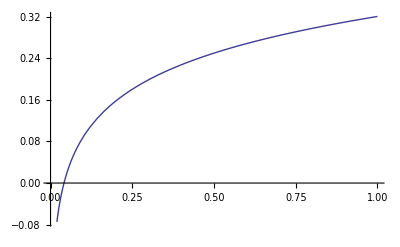

```mathematica
Plot[1/4(1-1/(8b)-1/b)+1/b(r^4/2+r^2)+C Log[2r]/.{b->1000,C->0.1},{r,0,1}]
```